## Curso de Mathematica (gbrayhan)

### Uso de Memoria en Mathematica

```mathematica
?MemoryInUse
```

MemoryInUse[] gives the number of bytes currently being used to store all data in the current Wolfram Language kernel session. 
MemoryInUse[$FrontEnd] gives the number of bytes used in the Wolfram System front end.

```mathematica
MemoryInUse[](*Este es un mensake que ignora el Kernel de Mathematica*)
```

173072160

```mathematica
mmu = MaxMemoryUsed[];NDSolve[{D[u[t,x],t,t]==D[u[t,x],x,x]+Sin[u[t,x]],u[0,x]==Exp[-x^2],(D[u[t,x],t] /. t->0)==0,u[t,-10]==u[t,10]},u,{t,0,10},{x,-10,10}]
```

{{u→InterpolatingFunction[{{0., 10.}, {…, -10., 10., …}}, <>]}}

```mathematica
MaxMemoryUsed[]- mmu
```

2351384

```mathematica
MemoryInUse[$FrontEnd]
```

163852

```mathematica
N[99060168/2^20]
```

94.4711

### Introduccion a DSolve - Ecuaciones Diferenciales

```mathematica
DSolve[{x''[t]==a,x'[0]==v0,x[0]==x0},x[t],t](*Resolviendo ecuaciones diferenciales*)
```

{{x[t]→1/2 (a t^2+2 t v0+2 x0)}}

```mathematica
x[t]/.{{x[t]->1/2 (a t^2+2 t v0+2 x0)}}
```

{1/2 (a t^2+2 t v0+2 x0)}

```mathematica
First[{1/2 (a t^2+2 t v0+2 x0)}]
```

1/2 (a t^2+2 t v0+2 x0)

### Ejemplos de Gráficas Simples

```mathematica
Manipulate[Plot[1/2 (a t^2+2 t v0+2 x0),{t,-8,8}],{a,-8,8},{v0,-2,2},{x0,-2,2}]
```

```mathematica
Plot3D[Sin[x y],{x,-Pi,Pi},{y,-Pi, Pi}, PlotPoints->25]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{r*Cos[theta],r*Sin[theta], BesselJ[2,r] Sin[2 theta] Cos[Pi]},{r, 0,5.13562},{theta,0,2 Pi},PlotPoints->25,BoxRatios->{1, 1, .4},ViewPoint->{2.34, -1.7, 1.6}]
```

-Graphics3D-

### Herramientas Matematicas

```mathematica
Expand[(x+y)^23](*Comentario en la ecuacion Ignorado por el Kernel*)
```

x^23+23 x^22 y+253 x^21 y^2+1771 x^20 y^3+8855 x^19 y^4+33649 x^18 y^5+100947 x^17 y^6+245157 x^16 y^7+490314 x^15 y^8+817190 x^14 y^9+1144066 x^13 y^10+1352078 x^12 y^11+1352078 x^11 y^12+1144066 x^10 y^13+817190 x^9 y^14+490314 x^8 y^15+245157 x^7 y^16+100947 x^6 y^17+33649 x^5 y^18+8855 x^4 y^19+1771 x^3 y^20+253 x^2 y^21+23 x y^22+y^23

### Ejemplod de aplicacion - “Matrices de Pauli”

```mathematica
pauliMatrix={{0,1},{1,0}};
```

```mathematica
Eigensystem[pauliMatrix]
```

{{-1,1},{{-1,1},{1,1}}}

### Informacion de Funciones y Palabras Reservadas

```mathematica
?Eigensystem
```

RowBox[{"Eigensystem", "[", StyleBox["m", "TI"], "]"}] gives a list RowBox[{"{", RowBox[{StyleBox["values", "TI"], ",", StyleBox["vectors", "TI"]}], "}"}] of the eigenvalues and eigenvectors of the square matrix StyleBox["m", "TI"]. 
RowBox[{"Eigensystem", "[", RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], "]"}] gives the generalized eigenvalues and eigenvectors of StyleBox["m", "TI"] with respect to StyleBox["a", "TI"]. 
RowBox[{"Eigensystem", "[", RowBox[{StyleBox["m", "TI"], ",", StyleBox["k", "TI"]}], "]"}] gives the eigenvalues and eigenvectors for the first StyleBox["k", "TI"] eigenvalues of StyleBox["m", "TI"]. 
RowBox[{"Eigensystem", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], ",", StyleBox["k", "TI"]}], "]"}] gives the first StyleBox["k", "TI"] generalized eigenvalues and eigenvectors.

```mathematica
??Eigensystem
```

Eigensystem[m] gives a list {values,vectors} of the eigenvalues and eigenvectors of the square matrix m. 
Eigensystem[{m,a}] gives the generalized eigenvalues and eigenvectors of m with respect to a. 
Eigensystem[m,k] gives the eigenvalues and eigenvectors for the first k eigenvalues of m. 
Eigensystem[{m,a},k] gives the first k generalized eigenvalues and eigenvectors.

Attributes[Eigensystem]={Protected}
 
Options[Eigensystem]={Cubics→False,Method→Automatic,Quartics→False,ZeroTest→Automatic}

```mathematica
?Eigensystem*
```

RowBox[{"Eigensystem", "[", StyleBox["m", "TI"], "]"}] gives a list RowBox[{"{", RowBox[{StyleBox["values", "TI"], ",", StyleBox["vectors", "TI"]}], "}"}] of the eigenvalues and eigenvectors of the square matrix StyleBox["m", "TI"]. 
RowBox[{"Eigensystem", "[", RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], "]"}] gives the generalized eigenvalues and eigenvectors of StyleBox["m", "TI"] with respect to StyleBox["a", "TI"]. 
RowBox[{"Eigensystem", "[", RowBox[{StyleBox["m", "TI"], ",", StyleBox["k", "TI"]}], "]"}] gives the eigenvalues and eigenvectors for the first StyleBox["k", "TI"] eigenvalues of StyleBox["m", "TI"]. 
RowBox[{"Eigensystem", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["m", "TI"], ",", StyleBox["a", "TI"]}], "}"}], ",", StyleBox["k", "TI"]}], "]"}] gives the first StyleBox["k", "TI"] generalized eigenvalues and eigenvectors.

```mathematica
?*Eigensystem*
```

RowBox[{"NDEigensystem", "[", RowBox[{RowBox[{StyleBox["ℒ", "TI"], "[", RowBox[{StyleBox["u", "TI"], "[", StyleBox[RowBox[{"x", ",", "y", ",", "…"}], "TI"], "]"}], "]"}], ",", StyleBox["u", "TI"], ",", RowBox[{StyleBox[RowBox[{"{", RowBox[{"x", ",", "y", ",", "…"}], "}"}], "TI"], "∈", StyleBox["Ω", "TR"]}], ",", StyleBox["n", "TI"]}], "]"}] gives the StyleBox["n", "TI"] smallest magnitude eigenvalues and eigenfunctions for the linear differential operator StyleBox["ℒ", "TI"] over the region StyleBox["Ω", "TR"].
RowBox[{RowBox[{"NDEigensystem", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{SubscriptBox[StyleBox["ℒ", "TI"], StyleBox["1", "TR"]], "[", RowBox[{RowBox[{StyleBox["u", "TI"], "[", StyleBox[RowBox[{"x", ",", "y", ",", "…"}], "TI"], "]"}], ",", RowBox[{StyleBox["v", "TI"], "[", StyleBox[RowBox[{"x", ",", "y", ",", "…"}], "TI"], "]"}], ",", StyleBox["…", "TR"]}], "]"}], ",", RowBox[{SubscriptBox[StyleBox["ℒ", "TI"], StyleBox["2", "TR"]], "[", RowBox[{RowBox[{StyleBox["u", "TI"], "[", StyleBox[RowBox[{"x", ",", "y", ",", "…"}], "TI"], "]"}], ",", RowBox[{StyleBox["v", "TI"], "[", StyleBox[RowBox[{"x", ",", "y", ",", "…"}], "TI"], "]"}], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["v", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{StyleBox[RowBox[{"{", RowBox[{"x", ",", "y", ",", "…"}], "}"}], "TI"], "∈", StyleBox["Ω", "TR"]}], ",", StyleBox["n", "TI"]}], "]"}], " "}] gives eigenvalues and eigenfunctions for the coupled differential operators RowBox[{"{", RowBox[{SubscriptBox[StyleBox["op", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["op", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}] over the region StyleBox["Ω", "TR"].
RowBox[{"NDEigensystem", "[", RowBox[{StyleBox["eqns", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["t", "TI"], ",", RowBox[{StyleBox[RowBox[{"{", RowBox[{"x", ",", "y", ",", "…"}], "}"}], "TI"], "∈", StyleBox["Ω", "TR"]}], ",", StyleBox["n", "TI"]}], "]"}] gives the eigenvalues and eigenfunctions in the spatial variables StyleBox[RowBox[{"{", RowBox[{"x", ",", "y", ",", "…"}], "}"}], "TI"] for solutions RowBox[{StyleBox["u", "TI"], ",", StyleBox["…", "TR"]}] of the coupled time-dependent differential equations StyleBox["eqns", "TI"].

```mathematica
Fibonacci[23,x]
```

1+66 x^2+715 x^4+3003 x^6+6435 x^8+8008 x^10+6188 x^12+3060 x^14+969 x^16+190 x^18+21 x^20+x^22

### Importando Paquetes a Mathematica

Instalar los paquetes en mathematica para windows es en la ruta ”C:\ProgramData\Mathematica\Applications”

```mathematica
<<xAct`xTensor`(*Otra forma de declarar es: Needs["PhysicalConstants`"]*)
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2015, Jose M. Martin-Garcia, under the General Public License.

Connecting to external linux executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.1.2, {2015,8,23}

CopyRight (C) 2002-2015, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
?Einstein
```

Einstein[covd] returns the Einstein curvature tensor associated to a metric-compatible connection covd acting on a tangent bundle.

```mathematica
<<xAct`xPerm`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2015, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

Connecting to external linux executable...

Connection established.

```mathematica
?xPermVerbose
```

xPermVerbose is an option for SchreierSims, RightCosetRepresentative, DoubleCosetRepresentative and CanonicalPerm. xPermVerbose->True gives lots of information about the intermediate status of the process.

### Notacion Cientifica

```mathematica
numero=0.000000012;
```

```mathematica
ScientificForm[numero]
```

1.2×10^-8

```mathematica
Clear[numero]
```

```mathematica
Precision[7/2]
```

∞

```mathematica
Precision[1/3]
```

∞

### Trabajar con Matrices

```mathematica
matriz={{2,4,6},{1,9,6},{4,3,2}};
```

```mathematica
MatrixForm[matriz]
```

(2 | 4 | 6
1 | 9 | 6
4 | 3 | 2)

```mathematica
matrizInvertida=Inverse[matriz];
```

```mathematica
matriz.matrizInvertida
```

```mathematica
{{1,0,0},{0,1,0},{0,0,1}}(**)
```

### Integrales Iteradas

```mathematica
(*Interesa el tercer resultado: 
Integrate[f,{x,xi,xf},{y,yi,yf},...] que equivale a: ∫_xi^xf ∫_yi^yf f(x,y)ⅆyⅆx
*)
```

Integrate[f,x] gives the indefinite integral ∫f dx. 
Integrate[f,{x,x_min,x_max}] gives the definite integral ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] gives the multiple integral ∫_x_min^x_max dx∫_y_min^y_max dy … f. 
Integrate[f,{x,y,…}∈reg] integrates over the geometric region reg.

Attributes[Integrate]={Protected,ReadProtected}
 
Options[Integrate]:={Assumptions:>$Assumptions,GenerateConditions→Automatic,PrincipalValue→False}

```mathematica
f[x_,y_]=y*x^2 +12xy +12;
Integrate[f[x,y],{x,-12,13},{y,-14,12}]
```

650/3 (-121+36 xy)

### Variables y Constantes Prefefinidas

```mathematica
Needs["PhysicalConstants`"]
```

General::obspkg: "PhysicalConstants`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
PlanckMass
```

2.17644×10^-8 Kilogram

```mathematica
t=(a+b)*(a-b)//Expand
```

a^2-b^2

```mathematica
t+b^2
```

a^2

```mathematica
Clear[t]
```

```mathematica
BoltzmannConstant
```

(1.38065×10^-23 Joule)/Kelvin

Clear All of mathematica variables

```mathematica
Clear["Global`*"]
```

```mathematica
2x+23y/.x->32
```

64+23 y

```mathematica
x(*No se asigna ningun valor previo a x*)
```

x

```mathematica
??Constants
```

Constants is an option for Dt which gives a list of objects to be taken as constants.

Attributes[Constants]={Protected}

### Importando paquete de constantes Físicas (Full compatible whit mathemathica 9)

```mathematica
<<PhysicalConstants`
```

General::obspkg: "PhysicalConstants`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
PlanckConstant
```

PlanckConstant

```mathematica
Information[PlanckConstant]
```

Global`PlanckConstant

```mathematica
UnitConvert[Quantity[1,"PlanckConstant"],"SIBase"]
```

6.62607×10^-34 kg m^2/s

```mathematica
listAdd[structured_,flat_]:=Module[{i=1},Function[elm,elm+flat[[i++]],{Listable}][structured]]
listAdd[{{a,b},{c},{d,e,f}},{1,2,3,4,5,6}]
(*   {{1+a,2+b},{3+c},{4+d,5+e,6+f}}   *)
```

{{1+a,2+b},{3+c},{4+d,5+e,6+f}}

### Herramientas de Variable Compleja

```mathematica
ComplexExpand[E^(10 x *I) *Sin[x+I y]]
```

Cos[10 x] Cosh[y] Sin[x]-Cos[x] Sin[10 x] Sinh[y]+ⅈ (Cosh[y] Sin[x] Sin[10 x]+Cos[x] Cos[10 x] Sinh[y])

```mathematica
TrigToExp[Cos[10 x] Cosh[y] Sin[x]-Cos[x] Sin[10 x] Sinh[y]+ⅈ (Cosh[y] Sin[x] Sin[10 x]+Cos[x] Cos[10 x] Sinh[y])]
```

-1/2 ⅈ ⅇ^(11 ⅈ x-y)+1/2 ⅈ ⅇ^(9 ⅈ x+y)

```mathematica
Simplify[Cos[x]^2 +Sin[x]^2]
```

1

```mathematica
Simplify[Log[x^r]]
```

Log[x^r]

```mathematica
Simplify[Log[x^r],x>0 && r∈Reals ]
```

r Log[x]

Reduce el grado de las expresiones trigonometricas

```mathematica
TrigReduce[Sin[x]^3 * Cos[y]^2]
```

1/16 (6 Sin[x]-2 Sin[3 x]+3 Sin[x-2 y]-Sin[3 x-2 y]+3 Sin[x+2 y]-Sin[3 x+2 y])

```mathematica
ComplexExpand[ExpToTrig[E^(x + I y)]]
```

Cos[y] Cosh[x]+Cos[y] Sinh[x]+ⅈ (Cosh[x] Sin[y]+Sin[y] Sinh[x])

#### Ejemplo de una simplificación definida

```mathematica
Simplify[Cos[(n Pi/2)-x]]
```

Cos[(n π)/2-x]

```mathematica
Simplify[Cos[(n Pi/2)-x],(n-1)/4∈Integers ](*Empleando criterios de definición*)
```

Sin[x]

### Teorema de DeMovrie usando Mathematica

```mathematica
Clear[n]
```

```mathematica
z=r(Cos[θ]+I Sin[θ]);
FullSimplify[z^n,r≥ 0 && n>0 && n∈Integers]
```

(ⅇ^(ⅈ θ) r)^n

```mathematica
PowerExpand[(ⅇ^(ⅈ θ) r)^n]
```

ⅇ^(ⅈ n θ) r^n

```mathematica
ExpToTrig[ⅇ^(ⅈ n θ) r^n]
```

r^n Cos[n θ]+ⅈ r^n Sin[n θ]

```mathematica
Factor[r^n Cos[n θ]+ⅈ r^n Sin[n θ]]
```

r^n (Cos[n θ]+ⅈ Sin[n θ])

### Graficas de Variable Compleja

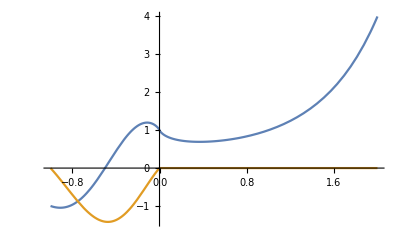

```mathematica
Plot[{Re[x^x],Im[x^x]},{x,-1,2},PlotRange->All]
```

```mathematica
x2x[0.0,_]=x2x[0,_]=1;
x2x[x_,k_]:=Exp[x (Log[x]+2 I Pi k)];
Table[points3D[k]=Table[z=x2x[x,k];
{x,Re[z],Im[z]},{x,-4,2,0.005}],{k,-7,7}];
Graphics3D[Table[{If[k==0,Thick,Opacity[0.5]],Line[points3D[k]]},{k,-4,4}],Axes->True,PlotRange->{{-4,2},{-4,4},{-4,4}},BoxRatios->{2,1,1},ViewPoint->{2,2,12},ViewVertical->{0,1,0}]
```

-Graphics3D-

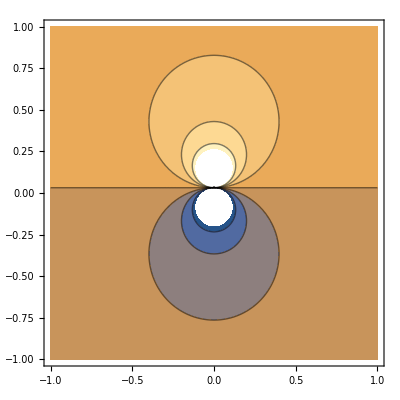
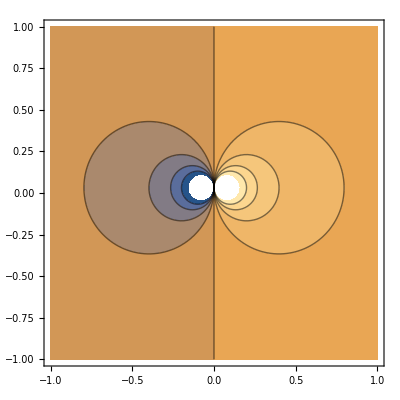

```mathematica
eqn[x_,y_]:=(25 Pi (x+I y) I)/(1+10 Pi (x+I y) I)

{ContourPlot[Re@eqn[x,y],{x,-1,1},{y,-1,1},PlotPoints->50],ContourPlot[Im@eqn[x,y],{x,-1,1},{y,-1,1},PlotRange->{-0.5,0.5},PlotPoints->50]}
```

```mathematica
Plot3D[Abs[eqn[x,y]],{x,-1,1},{y,-1,1},PlotPoints->40]
```

-Graphics3D-

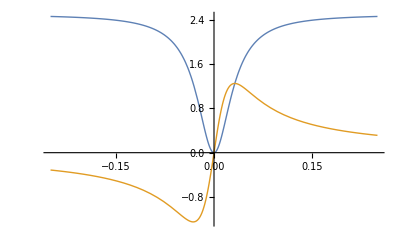

```mathematica
eqnR[x_]:=(25 Pi x I)/(1+10 Pi x I)
Plot[{Tooltip@Re@eqnR[x],Tooltip@Im@eqnR[x]},{x,-0.25,0.25},PlotStyle->Thick,PlotRange->All]
```

### Sistemas de Ecuaciones (NSolve)

```mathematica
NSolve[x^4 -3x^3+1==0,x](*Ejemplo con una variable*)
```

{{x→-0.363163-0.556424 ⅈ},{x→-0.363163+0.556424 ⅈ},{x→0.764826},{x→2.9615}}

#### Visualizando la solucion de la ecuación

```mathematica
f[x_]=x^4 -3x^3+1
```

1-3 x^3+x^4

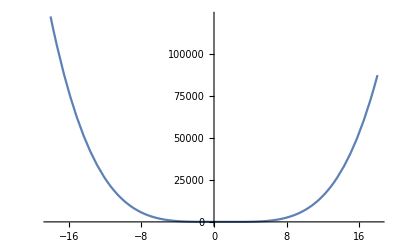

```mathematica
Plot[1-3 x^3+x^4,{x,-18.,18.}]
```

#### Otro Ejemplo

```mathematica
NSolve[{2x+3y==3,21x+y==9},{x,y}](*Ejemplo con dos variables*)
```

{{x→0.393443,y→0.737705}}

```mathematica
??NDSolveValue
```

NDSolveValue[eqns,expr,{x,x_min,x_max}] gives the value of expr with functions determined by a numerical solution to the ordinary differential equations eqns with the independent variable x in the range x_min to x_max. 
NDSolveValue[eqns,expr,{x,x_min,x_max},{y,y_min,y_max}] solves the partial differential equations eqns over a rectangular region.
NDSolveValue[eqns,expr,{x,y}∈Ω] solves the partial differential equations eqns over the region Ω.
NDSolveValue[eqns,u,{t,t_min,t_max},{x,y}∈Ω] solves the time-dependent partial differential equations eqns over the region Ω.

Attributes[NDSolveValue]={Protected}
 
Options[NDSolveValue]={AccuracyGoal→Automatic,Compiled→Automatic,DependentVariables→Automatic,DiscreteVariables→{},EvaluationMonitor→None,InterpolationOrder→Automatic,MaxStepFraction→1/10,MaxSteps→Automatic,MaxStepSize→Automatic,Method→Automatic,NormFunction→Automatic,PrecisionGoal→Automatic,StartingStepSize→Automatic,StepMonitor→None,WorkingPrecision→MachinePrecision}

```mathematica
sol=NDSolveValue[{x''[t] -0.5(1-x[t]^(2))*x'[t] +x[t]==0,x'[0]==0,x[0]==1.5   },x,{t,0,7*Pi}]
```

InterpolatingFunction[{{0., 21.9911}}, <>]

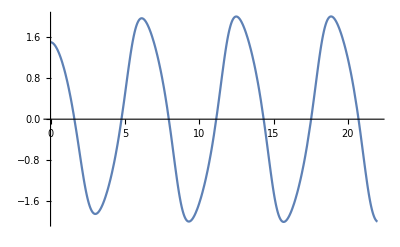

```mathematica
Plot[sol[x],{x,0.,21.991148575128552}]
```

### Series e Integrales

```mathematica
??Series
```

Series[f,{x,x_0,n}] generates a power series expansion for f about the point x=x_0 to order (x-x_0)^n. 
Series[f,{x,x_0,n_x},{y,y_0,n_y},…] successively finds series expansions with respect to x, then y, etc.

Attributes[Series]={Protected}
 
Options[Series]={Analytic→True,Assumptions:>$Assumptions}

```mathematica
Series[(1-x^4)^2,{x,0,8}]
```

1-2 x^4+x^8+O[x]^9

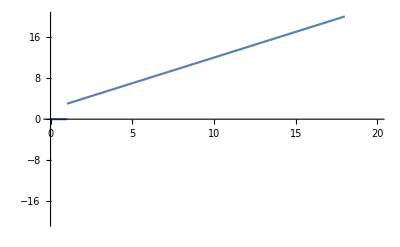

```mathematica
f[t_]:=(t+2)HeavisideTheta[t-1];
Plot[f[t],{t,0,20},PlotRange->{-20,20}]
```

```mathematica
g[t_]=FourierSeries[f[t],t,2]//ExpToTrig
```

1-5/(4 π)+π/4-Cos[t]/π-(Cos[1] Cos[t])/π+Cos[2 t]/(4 π)-(Cos[2] Cos[2 t])/(4 π)-(3 Cos[t] Sin[1])/π-(3 Cos[2 t] Sin[2])/(2 π)+Sin[t]+(2 Sin[t])/π+(3 Cos[1] Sin[t])/π-(Sin[1] Sin[t])/π-1/2 Sin[2 t]-Sin[2 t]/π+(3 Cos[2] Sin[2 t])/(2 π)-(Sin[2] Sin[2 t])/(4 π)

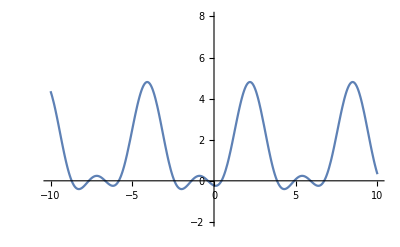

```mathematica
Plot[%,{t,-10,10},PlotRange->{-2,8}]
```

### Limites y Ecuaciones Diferenciales

```mathematica
Limit[(x^2 +1)/(x-1),x->1]
```

∞

```mathematica
Limit[Sin[2x],x->2]//N
```

-0.756802

```mathematica
DSolve[y''[x]+8y'[x]+16y[x]==12,y[x],x](*Vemos como existen constantes*)
```

{{y[x]→3/4+ⅇ^(-4 x) C[1]+ⅇ^(-4 x) x C[2]}}

```mathematica
DSolve[{y''[x]+8y'[x]+16y[x]==12,y[0]==2,y'[0]==1},y[x],x](*Desaparecen las constantes*)
```

{{y[x]→1/4 ⅇ^(-4 x) (5+3 ⅇ^(4 x)+24 x)}}

#### Sistema de Ecuaciones Diferenciales

```mathematica
DSolve[{x1''[t]+2 (ω^2)x1[t]-(ω^2)x2[t]==0,x2''[t]+2 (ω^2)x2[t]-(ω^2)x1[t]==0,x1'[0]==0,x2'[0]==0,x1[0]==0,x2[0]==a },{x1,x2},t]
```

{{x1→Function[{t},-1/4 a ⅇ^(-ⅈ t ω-ⅈ √3 t ω) (ⅇ^(ⅈ t ω)-ⅇ^(ⅈ √3 t ω)-ⅇ^(2 ⅈ t ω+ⅈ √3 t ω)+ⅇ^(ⅈ t ω+2 ⅈ √3 t ω))],x2→Function[{t},1/4 a ⅇ^(-ⅈ t ω-ⅈ √3 t ω) (ⅇ^(ⅈ t ω)+ⅇ^(ⅈ √3 t ω)+ⅇ^(2 ⅈ t ω+ⅈ √3 t ω)+ⅇ^(ⅈ t ω+2 ⅈ √3 t ω))]}}

```mathematica
-1/4 a ⅇ^(-ⅈ t ω-ⅈ √3 t ω) (ⅇ^(ⅈ t ω)-ⅇ^(ⅈ √3 t ω)-ⅇ^(2 ⅈ t ω+ⅈ √3 t ω)+ⅇ^(ⅈ t ω+2 ⅈ √3 t ω))//ExpToTrig
```

```mathematica
-1/4 a (Cos[t ω+√3 t ω]-ⅈ Sin[t ω+√3 t ω]) (Cos[t ω]-Cos[√3 t ω]-Cos[2 t ω+√3 t ω]+Cos[t ω+2 √3 t ω]+ⅈ Sin[t ω]-ⅈ Sin[√3 t ω]-ⅈ Sin[2 t ω+√3 t ω]+ⅈ Sin[t ω+2 √3 t ω])//FullSimplify
```

1/2 a (Cos[t ω]-Cos[√3 t ω])

```mathematica
Manipulate[Plot[1/2 a (Cos[t ω]-Cos[√3 t ω]),{t,-8,8}],{a,-8,8},{ω,-2,2}]
```

### Funciones Definidas

```mathematica
f[x_,y_]:=x^2 * y^3 +x y+2x-3y
f[x,2]
```

-6+4 x+8 x^2

```mathematica
D[f[x, y], x, x, y]
```

6 y^2

WolframAlphaQueryResults

6 y^2

#### Ejemplo de la Ecuacion de Schrodinger

```mathematica
H[V_]@ψ_:=(-ℏ^2 /2m)*D[ψ,{x,2}] +V ψ
```

```mathematica
H[V[x]]@ψ[x]==Energy*ψ[x]
```

V[x] ψ[x]-1/2 m ℏ^2 ψ''[x]==Energy ψ[x]

### Transformada de Fourier

```mathematica
?FourierTransform
```

FourierTransform[expr,t,ω] gives the symbolic Fourier transform of expr. 
FourierTransform[expr,{t_1,t_2,…},{ω_1,ω_2,…}] gives the multidimensional Fourier transform of expr.

```mathematica
??FourierParameters
```

FourierParameters is an option to Fourier and related functions that specifies the conventions to use in computing Fourier transforms.

Attributes[FourierParameters]={Protected,ReadProtected}

```mathematica
?*InverseFourierTransform
```

RowBox[{"InverseFourierTransform", "[", RowBox[{StyleBox["expr", "TI"], ",", "ω", ",", StyleBox["t", "TI"]}], "]"}] gives the symbolic inverse Fourier transform of StyleBox["expr", "TI"]. 
RowBox[{"InverseFourierTransform", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox["ω", StyleBox["1", "TR"]], ",", SubscriptBox["ω", StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["t", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["t", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] gives the multidimensional inverse Fourier transform of StyleBox["expr", "TI"].

```mathematica
??DiracDelta
```

RowBox[{"DiracDelta", "[", StyleBox["x", "TI"], "]"}] represents the Dirac delta function RowBox[{"δ", "(", StyleBox["x", "TI"], ")"}]. 
RowBox[{"DiracDelta", "[", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] represents the multidimensional Dirac delta function RowBox[{"δ", "(", RowBox[{SubscriptBox[StyleBox["x", "TI"], "1"], ",", SubscriptBox[StyleBox["x", "TI"], "2"], ",", "…"}], ")"}].

Attributes[DiracDelta]={Listable,Orderless,Protected,ReadProtected}

```mathematica
??UnitStep
```

RowBox[{"UnitStep", "[", StyleBox["x", "TI"], "]"}] represents the unit step function, equal to 0 for RowBox[{StyleBox["x", "TI"], "<", "0"}] and 1 for RowBox[{StyleBox["x", "TI"], "≥", "0"}]. 
RowBox[{"UnitStep", "[", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] represents the multidimensional unit step function which is 1 only if none of the SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]] are negative.

Attributes[UnitStep]={Listable,NumericFunction,Orderless,Protected,ReadProtected}

```mathematica
??HeavisideTheta
```

RowBox[{"HeavisideTheta", "[", StyleBox["x", "TI"], "]"}] represents the Heaviside theta function RowBox[{"θ", "(", StyleBox["x", "TI"], ")"}], equal to 0 for RowBox[{StyleBox["x", "TI"], "<", "0"}] and 1 for RowBox[{StyleBox["x", "TI"], ">", "0"}]. 
RowBox[{"HeavisideTheta", "[", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "]"}] represents the multidimensional Heaviside theta function, which is 1 only if none of the SubscriptBox[StyleBox["x", "TI"], StyleBox["i", "TI"]] are not positive.

Attributes[HeavisideTheta]={Listable,Orderless,Protected,ReadProtected}

Se observa que la diferencia entre UnitStep y HeavisideTheta es que HeavisideTheta no incluye al 0 en su definición estricta

```mathematica
??Piecewise
```

RowBox[{"Piecewise", "[", RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["2", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["2", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a piecewise function with values SubscriptBox[StyleBox["val", "TI"], StyleBox["i", "TI"]] in the regions defined by the conditions SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]]. 
RowBox[{"Piecewise", "[", RowBox[{RowBox[{"{", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["val", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["cond", "TI"], StyleBox["1", "TR"]]}], "}"}], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["val", "TI"]}], "]"}] uses default value StyleBox["val", "TI"] if none of the SubscriptBox[StyleBox["cond", "TI"], StyleBox["i", "TI"]] apply. The default for StyleBox["val", "TI"] is 0.

Attributes[Piecewise]={HoldAll,Protected,ReadProtected}
 
Piecewise/:Default[Piecewise,2]:=0

#### Ejemplos de Transformada de Fourier

```mathematica
Clear[Global]
```

```mathematica
f[t_]:=E^(t-1) * Sin[Pi *t];
```

```mathematica
f[t]
```

ⅇ^(-1+t) Sin[π t]

```mathematica
LaplaceTransform[f[t],t,ω]//ExpandDenominator
```

π/(ⅇ+ⅇ π^2-2 ⅇ ω+ⅇ ω^2)

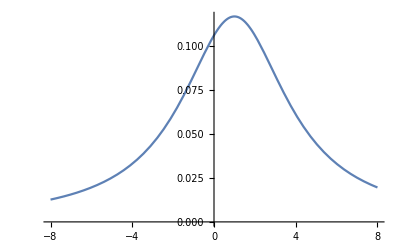

```mathematica
Plot[π/(ⅇ+ⅇ π^2-2 ⅇ ω+ⅇ ω^2),{ω,-8,8}]
```

```mathematica
??Factor
```

Factor[poly] factors a polynomial over the integers. 
Factor[poly,Modulus→p] factors a polynomial modulo a prime p. 
Factor[poly,Extension→{a_1,a_2,…}] factors a polynomial allowing coefficients that are rational combinations of the algebraic numbers a_i.

Attributes[Factor]={Listable,Protected}
 
Options[Factor]={Extension→None,GaussianIntegers→False,Modulus→0,Trig→False}

```mathematica
FourierTransform[DiracDelta[t+2],t,ω]
```

ⅇ^(-2 ⅈ ω)/(√(2 π))

```mathematica
Sin[2x]*TrigReduce[Sin[x]^2]//TrigToExp//Simplify
```

1/8 ⅈ ⅇ^(-4 ⅈ x) (-1+ⅇ^(2 ⅈ x))^3 (1+ⅇ^(2 ⅈ x))

```mathematica
Options[FourierTransform]
```

{Assumptions:>$Assumptions,GenerateConditions→False,FourierParameters→{0,1}}